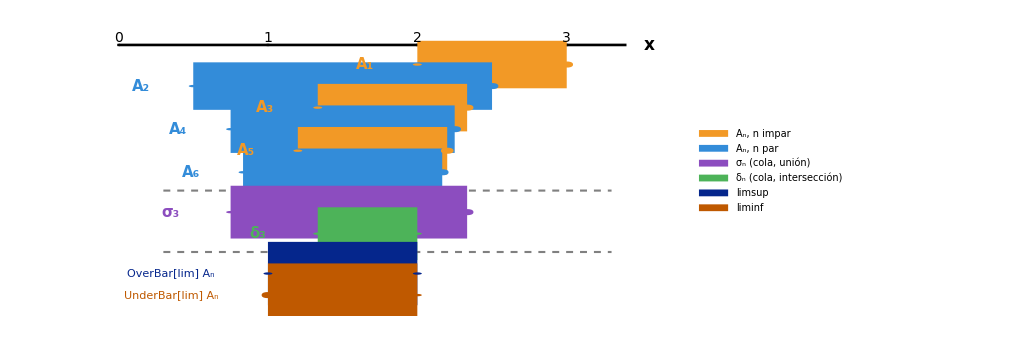

```mathematica
nMin=1;nMax=6;
sep=0.55;

leftA[n_]:=1-(-1)^n/n;
rightA[n_]:=2+1/n;

colorImpar=RGBColor[0.95,0.6,0.15];
colorPar=RGBColor[0.2,0.55,0.85];
colorSigma=RGBColor[0.55,0.3,0.75];
colorDelta=RGBColor[0.3,0.7,0.35];
colorLimsup=RGBColor[0.02,0.15,0.55];
colorLiminf=RGBColor[0.75,0.35,0.0];

subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

rDot=0.03;
closedDot[center_,col_]:={col,Disk[center,rDot]};
openDot[center_,col_]:={White,Disk[center,rDot],col,Thickness[0.0035],Circle[center,rDot]};

(*----------filas A_n,n=1,...,6----------*)
filasA=Table[Module[{y,xl,xr,col},y=-(n-nMin) sep;
xl=leftA[n];xr=rightA[n];
col=If[OddQ[n],colorImpar,colorPar];
{col,Thickness[0.045],CapForm["Round"],Line[{{xl,y},{xr,y}}],closedDot[{xl,y},col],openDot[{xr,y},col],Text[Style["A"<>subInd[n],15,Bold],{xl-0.35,y}]}],{n,nMin,nMax}];

yUltimaA=-(nMax-nMin) sep;

(*----------filas sigma_n,delta_n para un n de muestra (apartado a)----------*)
nMuestra=3;
sigmaVal={1-1/(2 Ceiling[nMuestra/2]),2+1/nMuestra};
deltaVal={1+1/(2 Ceiling[nMuestra/2]-1),2};

ySep1=yUltimaA-0.85 sep;
ySigma=ySep1-sep;
yDelta=ySigma-sep;

filaSigma={colorSigma,Thickness[0.05],CapForm["Round"],Line[{{sigmaVal[[1]],ySigma},{sigmaVal[[2]],ySigma}}],closedDot[{sigmaVal[[1]],ySigma},colorSigma],openDot[{sigmaVal[[2]],ySigma},colorSigma],Text[Style["σ"<>subInd[nMuestra],15,Bold],{sigmaVal[[1]]-0.4,ySigma}]};

filaDelta={colorDelta,Thickness[0.05],CapForm["Round"],Line[{{deltaVal[[1]],yDelta},{deltaVal[[2]],yDelta}}],closedDot[{deltaVal[[1]],yDelta},colorDelta],closedDot[{deltaVal[[2]],yDelta},colorDelta],Text[Style["δ"<>subInd[nMuestra],15,Bold],{deltaVal[[1]]-0.4,yDelta}]};

lineaSep1={Gray,Dashed,Thickness[0.002],Line[{{0.3,ySep1},{3.3,ySep1}}]};

(*----------filas resumen:limsup,liminf----------*)
ySep2=yDelta-0.85 sep;
yLimsup=ySep2-sep;
yLiminf=yLimsup-sep;

filaLimsup={colorLimsup,Thickness[0.06],CapForm["Round"],Line[{{1,yLimsup},{2,yLimsup}}],closedDot[{1,yLimsup},colorLimsup],closedDot[{2,yLimsup},colorLimsup],Text[Row[{OverBar[Style["lim",15,Bold]],Style[" Aₙ",15,Bold]}],{0.35,yLimsup}]};

filaLiminf={colorLiminf,Thickness[0.06],CapForm["Round"],Line[{{1,yLiminf},{2,yLiminf}}],openDot[{1,yLiminf},colorLiminf],closedDot[{2,yLiminf},colorLiminf],Text[Row[{UnderBar[Style["lim",15,Bold]],Style[" Aₙ",15,Bold]}],{0.35,yLiminf}]};

lineaSep2={Gray,Dashed,Thickness[0.002],Line[{{0.3,ySep2},{3.3,ySep2}}]};

(*----------eje real----------*)
xMaxPlot=3.4;
ejeReal={Black,Thickness[0.0025],Line[{{0,0.5},{xMaxPlot,0.5}}],Table[Line[{{k,0.47},{k,0.53}}],{k,0,3}],Table[Text[Style[k,14],{k,0.68}],{k,0,3}],Text[Style["x",17,Bold],{xMaxPlot+0.15,0.5}]};

grafico=Graphics[{ejeReal,filasA,lineaSep1,filaSigma,filaDelta,lineaSep2,filaLimsup,filaLiminf},PlotRange->{{-0.2,xMaxPlot+0.3},{yLiminf-0.4,0.85}},AspectRatio->0.45,ImageSize->760];

leyenda=SwatchLegend[{colorImpar,colorPar,colorSigma,colorDelta,colorLimsup,colorLiminf},{"Aₙ, n impar","Aₙ, n par","σₙ (cola, unión)","δₙ (cola, intersección)","limsup","liminf"},LabelStyle->Directive[FontSize->14],LegendMarkerSize->18];

imagenCompleta=Legended[grafico,leyenda];

imagenCompleta
```

```mathematica
Export["propuesto1_P1.png",imagenCompleta,Background->White,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["propuesto1_P1.png"]]]
```